```mathematica
trainingData=Import["C:\\Users\\Honzaik\\la2_du\\ukol2\\train.csv"]
```

{{2018-04-08,40,11},{2018-04-15,40,11},{2018-04-22,39,11},{2018-04-29,38,11},{2018-05-06,40,10},{2018-05-13,34,10},{2018-05-20,34,11},{2018-05-27,32,11},{2018-06-03,35,11},{2018-06-10,32,11},{2018-06-17,33,11},{2018-06-24,38,11},{2018-07-01,32,12},{2018-07-08,33,12},{2018-07-15,35,12},{2018-07-22,35,12},{2018-07-29,31,12},{2018-08-05,36,12},{2018-08-12,35,12},{2018-08-19,40,12},{2018-08-26,45,12},{2018-09-02,47,12},{2018-09-09,47,11},{2018-09-16,48,11},{2018-09-23,55,12},{2018-09-30,58,27},{2018-10-07,59,17},{2018-10-14,59,13},{2018-10-21,65,12},{2018-10-28,77,13},{2018-11-04,100,12},{2018-11-11,44,12},{2018-11-18,32,13},{2018-11-25,39,13},{2018-12-02,38,14},{2018-12-09,38,14},{2018-12-16,33,13},{2018-12-23,25,12},{2018-12-30,27,14},{2019-01-06,37,13},{2019-01-13,39,13},{2019-01-20,40,13},{2019-01-27,37,13},{2019-02-03,41,12},{2019-02-10,40,14},{2019-02-17,39,20},{2019-02-24,40,12}}

```mathematica
trainPol=trainingData[[All,2]]
```

{40,40,39,38,40,34,34,32,35,32,33,38,32,33,35,35,31,36,35,40,45,47,47,48,55,58,59,59,65,77,100,44,32,39,38,38,33,25,27,37,39,40,37,41,40,39,40}

```mathematica
trainToil=trainingData[[All,3]]
```

{11,11,11,11,10,10,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,11,11,12,27,17,13,12,13,12,12,13,13,14,14,13,12,14,13,13,13,13,12,14,20,12}

```mathematica
Length[trainPol]
```

47

{{11,11},{11,11},{11,11},{10,11},{10,10},{11,10},{11,11},{11,11},{11,11},{11,11},{11,11},{12,11},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{11,12},{11,11},{12,11},{27,12},{17,27},{13,17},{12,13},{13,12},{12,13},{12,12},{13,12},{13,13},{14,13},{14,14},{13,14},{12,13},{14,12},{13,14},{13,13},{13,13},{13,13},{12,13},{14,12},{20,14},{12,20}}

{5212828/3506977,6204148/3506977}

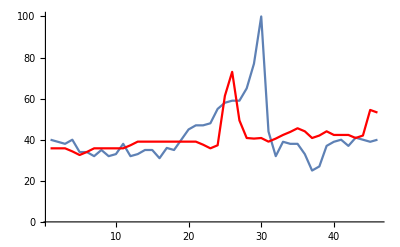

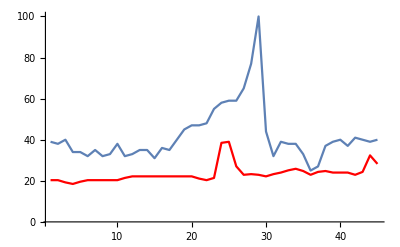

{{12,12,12,12,12,12,12,12,11,11,11,11,11,11,10,10,11,11,11,11},{12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,10,10,11,11,11},{12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,10,10,11,11},{11,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,10,10,11},{11,11,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,10,10},{12,11,11,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,10},{27,12,11,11,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11},{17,27,12,11,11,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11},{13,17,27,12,11,11,12,12,12,12,12,12,12,12,12,12,11,11,11,11},{12,13,17,27,12,11,11,12,12,12,12,12,12,12,12,12,12,11,11,11},{13,12,13,17,27,12,11,11,12,12,12,12,12,12,12,12,12,12,11,11},{12,13,12,13,17,27,12,11,11,12,12,12,12,12,12,12,12,12,12,11},{12,12,13,12,13,17,27,12,11,11,12,12,12,12,12,12,12,12,12,12},{13,12,12,13,12,13,17,27,12,11,11,12,12,12,12,12,12,12,12,12},{13,13,12,12,13,12,13,17,27,12,11,11,12,12,12,12,12,12,12,12},{14,13,13,12,12,13,12,13,17,27,12,11,11,12,12,12,12,12,12,12},{14,14,13,13,12,12,13,12,13,17,27,12,11,11,12,12,12,12,12,12},{13,14,14,13,13,12,12,13,12,13,17,27,12,11,11,12,12,12,12,12},{12,13,14,14,13,13,12,12,13,12,13,17,27,12,11,11,12,12,12,12},{14,12,13,14,14,13,13,12,12,13,12,13,17,27,12,11,11,12,12,12},{13,14,12,13,14,14,13,13,12,12,13,12,13,17,27,12,11,11,12,12},{13,13,14,12,13,14,14,13,13,12,12,13,12,13,17,27,12,11,11,12},{13,13,13,14,12,13,14,14,13,13,12,12,13,12,13,17,27,12,11,11},{13,13,13,13,14,12,13,14,14,13,13,12,12,13,12,13,17,27,12,11},{12,13,13,13,13,14,12,13,14,14,13,13,12,12,13,12,13,17,27,12},{14,12,13,13,13,13,14,12,13,14,14,13,13,12,12,13,12,13,17,27},{20,14,12,13,13,13,13,14,12,13,14,14,13,13,12,12,13,12,13,17},{12,20,14,12,13,13,13,13,14,12,13,14,14,13,13,12,12,13,12,13}}

{711946149670617386513471152660095805353441157563/552468860606317491637569403252148581578160457444,9844346413519209007775772360662378981152263154757/11049377212126349832751388065042971631563209148880,3602719912352992645324003373122480969424374054961/2762344303031587458187847016260742907890802287220,16801831439259744536767432505518507624976288558953/11049377212126349832751388065042971631563209148880,20757100587687378766545060184986816816998456244887/11049377212126349832751388065042971631563209148880,4663621888085560389158703492494765381556600282339/1381172151515793729093923508130371453945401143610,-4487717508845361714145810015892820357357906272243/5524688606063174916375694032521485815781604574440,-370933885064885499818543439758256945272180669868/690586075757896864546961754065185726972700571805,501497162499883583679515256843865472109425102239/5524688606063174916375694032521485815781604574440,-5435043757311357351391444201202018187768480884233/11049377212126349832751388065042971631563209148880,-205011928800127182528270628931851856605586943157/690586075757896864546961754065185726972700571805,-2229492923801951535398303647538762601273628858107/2762344303031587458187847016260742907890802287220,-14487154576327396819765584490588334717513640021373/11049377212126349832751388065042971631563209148880,-12138878491302002213667895994121607134997914138977/11049377212126349832751388065042971631563209148880,-333209552157480311987514673443452480245552618063/690586075757896864546961754065185726972700571805,-1814782340762813464768324540783506729282363111491/5524688606063174916375694032521485815781604574440,-81487826239820119641464721759601213705941727103/690586075757896864546961754065185726972700571805,-3838385638310210996255974050677843667820525898261/11049377212126349832751388065042971631563209148880,-1251718208319216472998502801297525913868366066671/5524688606063174916375694032521485815781604574440,-3721404715196846667903318841587620030703879417041/11049377212126349832751388065042971631563209148880}

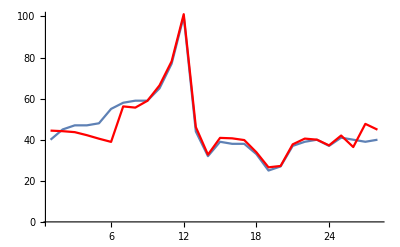

```mathematica
pocetVah=2;
b=trainPol[[2;;]];
A=Table[Table[trainToil[[i+j]],{j,pocetVah-1,0,-1}],{i,1,Length[b]}]
res=LeastSquares[A,b]
getEstimate[n_]:=res.Table[trainToil[[n-i]],{i,0,Length[res]-1}]
estimates=Table[getEstimate[i],{i,2,Length[trainPol]}];
gReal=ListLinePlot[trainPol[[2;;]],PlotRange->All];
gEst=ListLinePlot[estimates,PlotRange->All,PlotStyle->Red];
Show[gReal,gEst]
```

```mathematica
testData=Import["C:\\Users\\Honzaik\\la2_du\\ukol2\\test.csv"];
testToil=testData[[All,3]];
testPol=testData[[All,2]];
```

{-9579808891475352316/1001956072289065499,-71954603836159475574/7013692506023458493,-133869681981101466626/7013692506023458493,-155030725063491490838/7013692506023458493,60961699794124540337/7013692506023458493}

33.5427

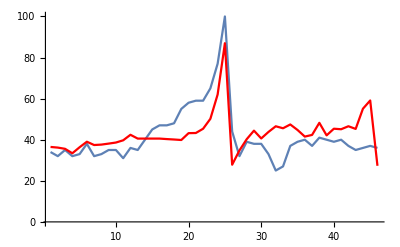

```mathematica
pocetVah=7;
b=trainPol[[pocetVah;;]];
A=Table[Table[trainToil[[i+j]],{j,pocetVah-1,0,-1}],{i,1,Length[b]}];
res=LeastSquares[A,b];
getEstimate[n_]:=res.Table[trainToil[[n-i]],{i,0,Length[res]-1}]
estimates=Table[getEstimate[i],{i,pocetVah,Length[trainPol]}];
gReal=ListLinePlot[trainPol[[pocetVah;;]],PlotRange->All];
gEst=ListLinePlot[estimates,PlotRange->All,PlotStyle->Red];
Show[gReal,gEst];
combinedToil=Join[trainToil,testToil];
getEstimate[n_]:=res.Table[combinedToil[[n-i]],{i,0,Length[res]-1}];
lReal=Join[trainPol,testPol][[pocetVah;;]];
lEst=Table[getEstimate[i],{i,pocetVah,Length[Join[trainPol,testPol]]}];
gReal=ListLinePlot[lReal,PlotRange->All];
gEst=ListLinePlot[lEst,PlotRange->All,PlotStyle->Red];
Take [(lReal-lEst),-Length[testPol]]
N[Norm[Take [(lReal-lEst),-Length[testPol]]]]
Show[gReal,gEst]
```